# Jupiter Satellite Position

## Summary:

The note book produces a “wavy-line” diagram of the four largest moons with respect to Jupiter as viewed from an input latitude and longitude on Earth.  Code is an application of the formulas given in Jean Meeus (1998). Astronomical Algorithms. Astronomical Algorithms book.

The plot is helpful for identifying the moon’s when viewing Jupiter, or for determining potential, “interesting” viewing times.  (Conjunctions, transits, occultations) The formula’s used for the calculations are low accuracy, and are not precises enough for calculating the exact times of the phenomena of the moons.

x: is measured positive to Jupiter’s west.
y: axis is set parrelle to Jupiter’s axis of rotation, with north positive.

Notebook sections

Functions: 
Formulas to determine the positions of Earth, Jupiter, and the four largest Julian moons.

Inputs:
Date to start the calculations.
Viewing Latitude and longitude
Total number of calculations

Variables:
year: calender year
month: number 1 to 12, starting month of the calculations
day:  starting calender day
hour: 0 - 24, starting time,  0 is the default.
n: number of calculations

Notes:
The calculations are low accuracy method [1]
A table is built for each moon via calculating the each moon’s position every four hours.


[1] Jean Meeus (1998). Astronomical Algorithms. Astronomical Algorithms, 2nd Edition (Willman-Bell Inc., Richmond, Virginia).

## Functions:

Calculate Julian Date

```mathematica
jd[y_,m_,d_,ut_]:=N[(Floor[365.25*(y+4716)]+Floor[30.6001*(m+1)]+d+(2-Floor[y/100]+Floor[Floor[y/100]/4])-1524.5)+ut/24,10]
```

Calculate days since January 1, 2000

```mathematica
dd[y_,m_,d_,ut_]:=With[{jd =  jd[y,m,d,ut]},jd- 2451545]
```

Long period term in the motion of Jupitier

```mathematica
v[y_,m_,d_,ut_]:=With[{ddd = dd[y,m,d,ut]},172.74 + 0.00111588 * ddd]
```

Mean anomalies of Earth / Jupiter

```mathematica
mm[y_,m_,d_,ut_]:=With[{ddd = dd[y,m,d,ut]},Mod[357.529 + 0.9856003*ddd,360]]
nn[y_,m_,d_,ut_]:=With[{ddd = dd[y,m,d,ut],vvv=v[y,m,d,ut]},Mod[20.020+ 0.0830853*ddd+.329*Sin[vvv Degree],360]]
```

```mathematica
nn[y_,m_,d_,ut_]:=With[{ddd = dd[y,m,d,ut],vvv=v[y,m,d,ut]},20.020+ 0.0830853*ddd+.329*Sin[vvv Degree]]
```

Difference between the mean heliocentric logitudes of Earth and Jupiter

```mathematica
jj[y_,m_,d_,ut_]:=With[{ddd = dd[y,m,d,ut],vvv=v[y,m,d,ut]},Mod[66.115+ 0.9025179*ddd-.329*Sin[vvv],360]]
```

Equations of the center of Earth and Jupiter in degrees

```mathematica
aa[y_,m_,d_,ut_]:=With[{mmm = mm[y,m,d,ut]},1.915*Sin[mmm Degree]+0.02*2*Sin[mmm Degree]*Cos[mmm Degree]]
bb[y_,m_,d_,ut_]:=With[{nnn= nn[y,m,d,ut]},5.555*Sin[nnn Degree]+0.168*2*Sin[nnn Degree]*Cos[nnn Degree]]
```

```mathematica
kk[y_,m_,d_,ut_]:=With[{jjj= jj[y,m,d,ut],aaa=aa[y,m,d,ut],bbb=bb[y,m,d,ut]},jjj+aaa-bbb]
```

Radius vector of Earth

```mathematica
re[y_,m_,d_,ut_]:=With[{mmm= mm[y,m,d,ut]},1.00014-0.01671*Cos[mmm Degree]-0.00014*(2*Cos[mmm Degree]^2-1)]
```

Radius vector of Jupiter

```mathematica
rj[y_,m_,d_,ut_]:=With[{nnn= nn[y,m,d,ut]},5.20872-0.25208*Cos[nnn Degree]-0.00611*(2*Cos[nnn Degree]^2-1)]
```

Distance Earth to Jupiter.

```mathematica
dist[y_,m_,d_,ut_]:=With[{ree= re[y,m,d,ut],rjj=rj[y,m,d,ut],kkk=kk[y,m,d,ut]},Sqrt[(ree^2+rjj^2-2*ree*rjj*Cos[kkk Degree])]]
```

Phase angle of Jupiter (Earth - Jupiter - Sun)

```mathematica
sψ[y_,m_,d_,ut_]:=With[{ree= re[y,m,d,ut],distt=dist[y,m,d,ut],kkk=kk[y,m,d,ut]},(ree/distt)*Sin[kkk Degree]]
```

```mathematica
ψ[y_,m_,d_,ut_]:=With[{ssψ= sψ[y,m,d,ut]},ArcSin[ssψ]/Degree]
```

Longitudes of the Central Meridian

```mathematica
ω1[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[210.98+877.8169088*(ddd-distt/173)+ψψ-bbb,360]]
```

```mathematica
ω2[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[187.23+870.1869088*(ddd-distt/173)+ψψ-bbb,360]]
```

Jupiter’s heliocentric Longitude

```mathematica
λ[y_,m_,d_,ut_]:=With[{vv= v[y,m,d,ut],ddd=dd[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[34.35+0.083091*ddd+0.329*Sin[vv Degree]+bbb,360]]
```

```mathematica
ds[y_,m_,d_,ut_]:=With[{λλ= λ[y,m,d,ut]},Mod[3.12*Sin[(λλ+42.8) Degree],360]]
```

```mathematica
de[y_,m_,d_,ut_]:=With[{λλ= λ[y,m,d,ut],ψψ= ψ[y,m,d,ut],rjj=rj[y,m,d,ut],distt=dist[y,m,d,ut],dss=ds[y,m,d,ut]},Mod[dss-2.22*Sin[ψψ Degree]*Cos[(λλ + 22)Degree]-(1.3*(rjj-distt)/distt)*Sin[(λλ -100.5)Degree],360]]
```

Calculate moon’s angle u measured to the inferior conjuction with Jupiter

```mathematica
u1[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[163.8069+203.4058646*(ddd-distt/173)+ψψ-bbb,360]]
```

```mathematica
u2[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[358.414+101.2916335*(ddd-distt/173)+ψψ-bbb,360]]
```

```mathematica
u3[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[5.7176+50.2345180*(ddd-distt/173)+ψψ-bbb,360]]
```

```mathematica
u4[y_,m_,d_,ut_]:=With[{ψψ= ψ[y,m,d,ut],ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut],bbb=bb[y,m,d,ut]},Mod[224.8092+21.48798000*(ddd-distt/173)+ψψ-bbb,360]]
```

```mathematica
gg[y_,m_,d_,ut_]:=With[{ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut]},Mod[331.18+50.310482*(ddd-distt/173),360]]
```

```mathematica
hh[y_,m_,d_,ut_]:=With[{ddd=dd[y,m,d,ut],distt=dist[y,m,d,ut]},Mod[87.45+21.569231*(ddd-distt/173),360]]
```

```mathematica
cu1[y_,m_,d_,ut_]:=With[{u11=u1[y,m,d,ut],u22=u2[y,m,d,ut]},Mod[0.473*Sin[2*(u11-u22) Degree],360]-360]
```

```mathematica
cu2[y_,m_,d_,ut_]:=With[{u22=u2[y,m,d,ut],u33=u3[y,m,d,ut]},Mod[1.065*Sin[2*(u22-u33) Degree],360]]
```

```mathematica
cu3[y_,m_,d_,ut_]:=With[{ggg=gg[y,m,d,ut]},Mod[0.165*Sin[ggg  Degree],360]]
```

```mathematica
cu4[y_,m_,d_,ut_]:=With[{hhh=hh[y,m,d,ut]},Mod[0.843*Sin[hhh  Degree],360]]
```

```mathematica
uu1[y_,m_,d_,ut_]:=With[{u11=u1[y,m,d,ut],cu11=cu1[y,m,d,ut]},u11+cu11]
```

```mathematica
uu2[y_,m_,d_,ut_]:=With[{u22=u2[y,m,d,ut],cu22=cu2[y,m,d,ut]},u22+cu22]
```

```mathematica
uu3[y_,m_,d_,ut_]:=With[{u33=u3[y,m,d,ut],cu33=cu3[y,m,d,ut]},u33+cu33]
```

```mathematica
uu4[y_,m_,d_,ut_]:=With[{u44=u4[y,m,d,ut],cu44=cu4[y,m,d,ut]},u44+cu44]
```

Calculate the moon’s radius to Jupieter

```mathematica
r1[y_,m_,d_,ut_]:=With[{u11=u1[y,m,d,ut],u22=u2[y,m,d,ut]},Mod[5.9057-0.0244*Cos[2*(u11-u22) Degree],360]]
```

```mathematica
r2[y_,m_,d_,ut_]:=With[{u22=u2[y,m,d,ut],u33=u3[y,m,d,ut]},Mod[9.3966-0.0244*Cos[2*(u22-u33) Degree],360]]
```

```mathematica
r3[y_,m_,d_,ut_]:=With[{ggg=gg[y,m,d,ut]},Mod[14.9883-0.0216*Cos[ggg  Degree],360]]
```

```mathematica
r4[y_,m_,d_,ut_]:=With[{hhh=hh[y,m,d,ut]},Mod[26.3627-0.1939*Cos[hhh  Degree],360]]
```

Calcuate the apparent x, y coordinates using the radius r, and angle uu (with corrections)

```mathematica
x1[y_,m_,d_,ut_]:=With[{r11=r1[y,m,d,ut],u11=u1[y,m,d,ut]},r11*Sin[u11 Degree]]
```

```mathematica
x2[y_,m_,d_,ut_]:=With[{r22=r2[y,m,d,ut],u22=u2[y,m,d,ut]},r22*Sin[u22 Degree]]
```

```mathematica
x3[y_,m_,d_,ut_]:=With[{r33=r3[y,m,d,ut],u33=u3[y,m,d,ut]},r33*Sin[u33 Degree]]
```

```mathematica
x4[y_,m_,d_,ut_]:=With[{r44=r4[y,m,d,ut],u44=u4[y,m,d,ut]},r44*Sin[u44 Degree]]
```

```mathematica
y1[y_,m_,d_,ut_]:=With[{r11=r1[y,m,d,ut],u11=u1[y,m,d,ut],dee=de[y,m,d,ut]},-r11*Cos[u11 Degree]*Sin[dee Degree]]
```

```mathematica
y2[y_,m_,d_,ut_]:=With[{r22=r2[y,m,d,ut],u22=u2[y,m,d,ut],dee=de[y,m,d,ut]},-r22*Cos[u22 Degree]*Sin[dee Degree]]
```

```mathematica
y3[y_,m_,d_,ut_]:=With[{r33=r3[y,m,d,ut],u33=u3[y,m,d,ut],dee=de[y,m,d,ut]},-r33*Cos[u33 Degree]*Sin[dee Degree]]
```

```mathematica
y4[y_,m_,d_,ut_]:=With[{r44=r4[y,m,d,ut],u44=u4[y,m,d,ut],dee=de[y,m,d,ut]},-r44*Cos[u44 Degree]*Sin[dee Degree]]
```

## Inputs

Replace the year, month, day, hour, and your latitude and longitude, as desired.

n is the number calculations,  a calcuations is made for each four hours.  ie..     4 hours * 6 * 30 = one month assuming 30 days / month

```mathematica
year=2015;
month=9;
day=1;
hour=0/(60*60*24);
n=30*6;
lat=N[FromDMS[{42,26,33}]];
lon=N[FromDMS[{83,29,7}]];
```

## Code

Create Empty list for results and date

```mathematica
date={};moon1={};moon2={};moon3={};moon4={};
```

```mathematica
Do[jday=jd[year,month,day,hour];

AppendTo[moon1,{x1[year,month,day,hour],jday}];
AppendTo[moon2,{x2[year,month,day,hour],jday}];
AppendTo[moon3,{x3[year,month,day,hour],jday}];
AppendTo[moon4,{x4[year,month,day,hour],jday}];
hour=hour+4;

,n]
```

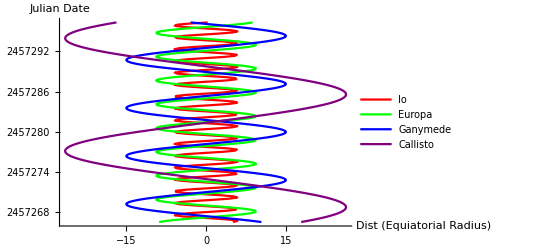

```mathematica
ListLinePlot[{moon1,moon2,moon3,moon4},PlotStyle->{Red,Green,Blue,Purple},PlotLegends->{"Io","Europa","Ganymede","Callisto"},AxesLabel->{"Dist (Equiatorial Radius)","Julian Date"}]
```